```mathematica
Needs["MazeNavigation`"]
Needs["VisualizeGenome`"]
```

## Create Map

```mathematica
map1=Rasterize[Graphics[{Antialiasing->False,Black,Thickness[0.05],Line[{{1,1},{20,1},{20,20},{1,20},{1,1}}],
Line[{{1,5},{20,10}}],
Line[{{1,6},{20,11}}]
}],RasterSize->{20,20}];
map1=(map1/.Graphics->List)[[1,1]]/.{{0,0,0}->1,{255,255,255}->0};
map1[[4,2]]=2;
map1[[15,15]]=3;
```

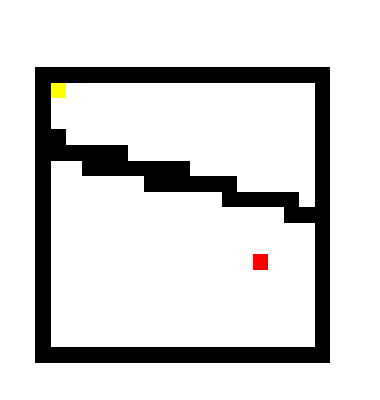

```mathematica
ArrayPlot[map1,ColorRules->{0->White,1->Black,2->Yellow,3->Red}]
```

```mathematica
Export["map1.csv",map1]
```

map1.csv

## Player

```mathematica
data=readAllFiles[{"GPAT_MAZE_MAP3_ORIG"}];
printAsTable[data,{"SOLVER"}]
expr=convertGPATGenome[sortConfigurationResults[data,"1","BSF",10,Output->"BSF"][[1,4]]]
```

ID | PARAM FILE | SOLVER
1 | GPAT_MAZE_MAP3_ORIG/parameters_001.txt | GPAT

{10.4729 x1 ArcTan[1.29963+3.96297 x2-4.81838 x5-1.22039 x6-1.62777 ArcTan[2 x0]]}

```mathematica
expr={Plus[-0.6469302754514258*x5]}
```

{-0.64693 x5}

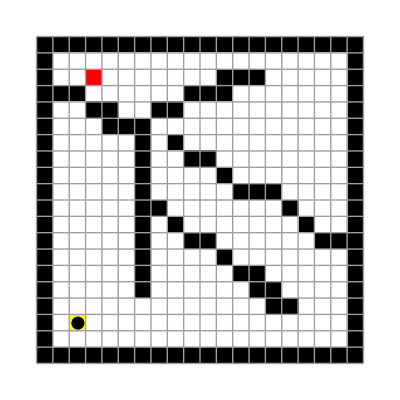

```mathematica
(state=loadMap["~/java/ne/cfg/demo/maze/map3.csv"])//showState
```

```mathematica
Manipulate[Nest[singleStep[#,expr]&,state,i]//showState,{i,0,100,1}]
```

```mathematica
data2=readAllFiles[{"GP_MAZE_MAP2_ORIG"}];
bestN=1;(*n-th best run*)
state2=loadMap["~/java/ne/cfg/demo/maze/map2.csv"];
printAsTable[data2,{"SOLVER"}]
expr2=
listBOGEvolution[Sequence@@(sortConfigurationResults[data2,"1","BSF",bestN,Output->"GenomeFileList"][[bestN]]),Choice->"Structural"];
Print[expr2//MatrixForm];
expr2=convertGPATGenome[expr2];
```

ID | PARAM FILE | SOLVER
1 | GP_MAZE_MAP2_ORIG/parameters_001.txt | GP

(1 | 98 | -1 | {x0} | 27.
2 | 200 | 62 | {x4} | 27.
3 | 295 | 51 | {gauss[plus[gauss[x3],atan[x5]]]} | 27.
4 | 400 | 255 | {x0} | 27.
5 | 498 | 223 | {plus[x4,-0.111443]} | 27.
6 | 566 | 3 | {sin[plus[times[plus[x6,-1.],x5],x6]]} | 28.
7 | 695 | 566 | {sin[plus[times[plus[x6,-1.],x2],x6]]} | 28.
8 | 800 | 51 | {gauss[x3]} | 27.
9 | 803 | 566 | {sin[plus[times[plus[x6,-1.],x5],x6]]} | 28.
10 | 990 | 803 | {sin[plus[times[plus[x6,-1.66569],x5],x6]]} | 28.
11 | 1077 | 803 | {sin[plus[times[plus[x6,-1.],x5],times[x3,x6]]]} | 28.
12 | 1200 | 928 | {x0} | 27.
13 | 1284 | 695 | {sin[plus[times[plus[x6,sin[-1.]],x2],x6]]} | 28.
14 | 1378 | 990 | {sin[plus[times[plus[x6,-1.66569],x5],x3]]} | 28.
15 | 1427 | 1077 | {sin[plus[times[plus[x6,-1.],x5],times[x1,x6]]]} | 37.
16 | 1583 | 990 | {sin[plus[times[plus[x6,-1.67939],x5],x6]]} | 28.
17 | 1687 | 1357 | {sin[plus[times[plus[x6,sin[-2.55425]],x2],x6]]} | 28.
18 | 1800 | 1670 | {sin[plus[times[plus[times[x6,x3],-1.66909],x5],x3]]} | 28.
19 | 1894 | 1734 | {sin[plus[times[plus[x6,sin[-1.]],plus[atan[x3],plus[x1,x0]]],x6]]} | 28.
20 | 1992 | 1668 | {sin[plus[times[plus[x1,-1.70138],x5],x6]]} | 28.
21 | 2035 | 1850 | {sin[plus[times[plus[sin[x4],-1.66569],x5],x1]]} | 37.
22 | 2197 | 2038 | {times[times[x2,-1.],plus[atan[sin[x0]],x1]]} | 28.
23 | 2295 | 2069 | {sin[plus[times[plus[x1,-1.6499],x5],x6]]} | 28.
24 | 2373 | 2035 | {sin[plus[times[plus[sin[x4],-1.66434],x5],x1]]} | 37.
25 | 2450 | 1427 | {sin[plus[times[plus[x6,-1.],x5],times[x1,x6]]]} | 37.
26 | 2581 | 1883 | {sin[plus[times[times[-1.,-4.97437],x1],x6]]} | 28.
27 | 2699 | 2038 | {times[times[x2,-1.],x0]} | 28.
28 | 2800 | 1701 | {sin[plus[times[plus[x6,-1.66909],x5],times[x3,x0]]]} | 28.
29 | 2882 | 1378 | {sin[plus[times[plus[x6,-1.66569],x5],x1]]} | 37.
30 | 2989 | 2373 | {sin[plus[times[plus[sin[x4],-1.7233],x5],x1]]} | 37.
31 | 3092 | 2945 | {sin[plus[times[plus[times[x3,-1.],-1.69787],x5],x1]]} | 37.
32 | 3186 | 1945 | {sin[plus[times[plus[x6,-1.65604],x5],x1]]} | 37.
33 | 3278 | 3063 | {sin[plus[times[plus[sin[x4],-1.66569],x5],atan[plus[x1,x3]]]]} | 37.
34 | 3400 | 3186 | {sin[plus[times[plus[x6,-1.65604],x5],sin[x1]]]} | 37.
35 | 3499 | 3184 | {sin[plus[times[-2.46626,x5],x1]]} | 37.
36 | 3599 | 3431 | {sin[plus[times[plus[x6,2.9741],x3],x1]]} | 37.
37 | 3697 | 3184 | {sin[plus[times[plus[-1.28801,-1.69787],x5],x1]]} | 37.
38 | 3704 | 3161 | {sin[sin[plus[x5,plus[plus[x5,x1],x3]]]]} | 40.)

```mathematica
{1,14,15,22,24,33,37,38}
```

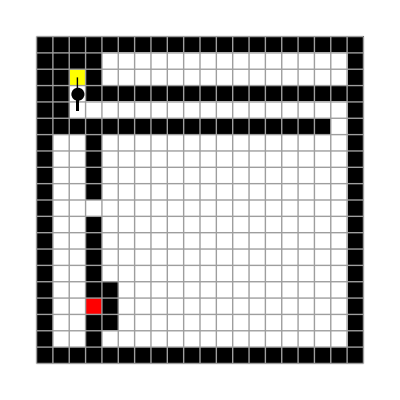
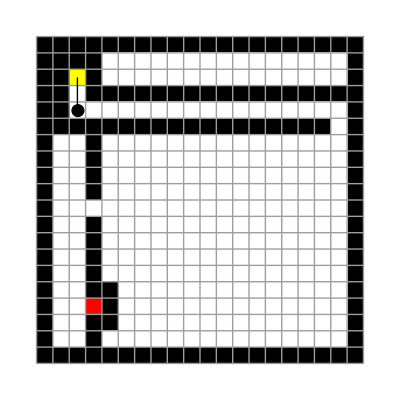
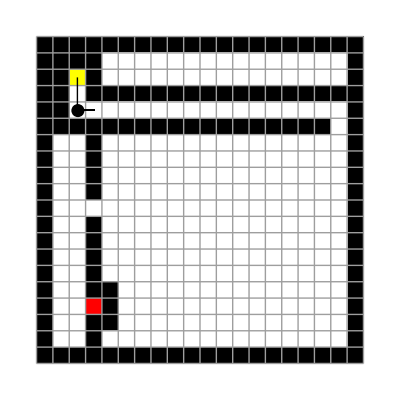
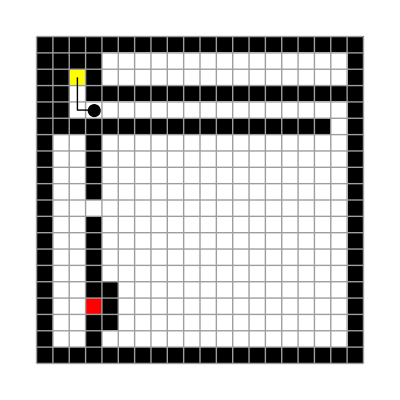
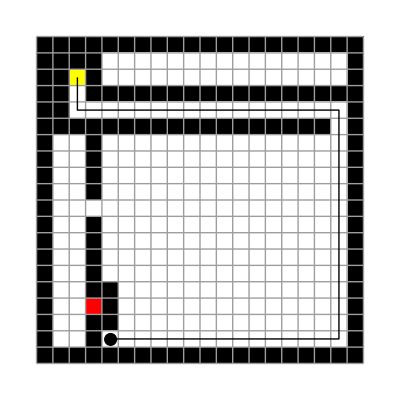
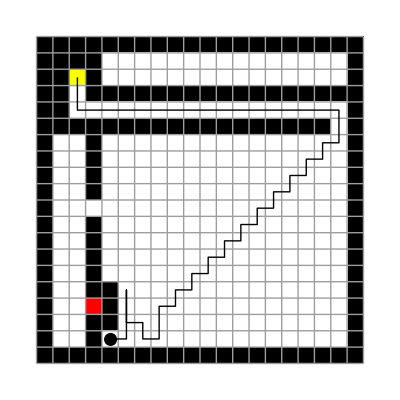
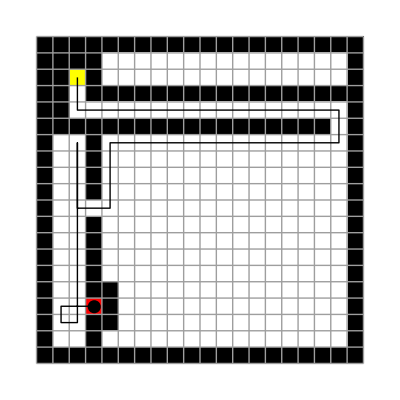
{-Graphics-
Generation 1
f = 27.,-Graphics-
Generation 2
f = 27.,-Graphics-
Generation 3
f = 27.,-Graphics-
Generation 4
f = 27.,-Graphics-
Generation 5
f = 27.,-Graphics-
Generation 6
f = 28.,-Graphics-
Generation 7
f = 28.,-Graphics-
Generation 8
f = 27.,-Graphics-
Generation 9
f = 28.,-Graphics-
Generation 10
f = 28.,-Graphics-
Generation 11
f = 28.,-Graphics-
Generation 12
f = 27.,-Graphics-
Generation 13
f = 28.,-Graphics-
Generation 14
f = 28.,-Graphics-
Generation 15
f = 37.,-Graphics-
Generation 16
f = 28.,-Graphics-
Generation 17
f = 28.,-Graphics-
Generation 18
f = 28.,-Graphics-
Generation 19
f = 28.,-Graphics-
Generation 20
f = 28.,-Graphics-
Generation 21
f = 37.,-Graphics-
Generation 22
f = 28.,-Graphics-
Generation 23
f = 28.,-Graphics-
Generation 24
f = 37.,-Graphics-
Generation 25
f = 37.,-Graphics-
Generation 26
f = 28.,-Graphics-
Generation 27
f = 28.,-Graphics-
Generation 28
f = 28.,-Graphics-
Generation 29
f = 37.,-Graphics-
Generation 30
f = 37.,-Graphics-
Generation 31
f = 37.,-Graphics-
Generation 32
f = 37.,-Graphics-
Generation 33
f = 37.,-Graphics-
Generation 34
f = 37.,-Graphics-
Generation 35
f = 37.,-Graphics-
Generation 36
f = 37.,-Graphics-
Generation 37
f = 37.,-Graphics-
Generation 38
f = 40.}

```mathematica
grid=Grid[{{simulateToTarget[state2,#[[4]],120]},{"Generation "<>ToString[#[[1]]]}, {Style["f = "<>ToString[#[[5]]],Italic]}}]&/@expr2
```

```mathematica
MapIndexed[Export["110817_visualizeRun_MAP_"<>ToString[Sequence@@#2+11]<>".pdf",#1]&,grid[[{1,14,15,22,24,33,37,38}]]]
```

{110817_visualizeRun_MAP_12.pdf,110817_visualizeRun_MAP_13.pdf,110817_visualizeRun_MAP_14.pdf,110817_visualizeRun_MAP_15.pdf,110817_visualizeRun_MAP_16.pdf,110817_visualizeRun_MAP_17.pdf,110817_visualizeRun_MAP_18.pdf,110817_visualizeRun_MAP_19.pdf}